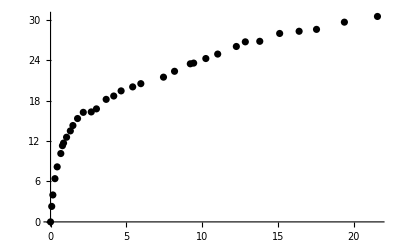

```mathematica
(*T=373-345*)
V01 = 1.62;
bases1 = {V01, 1.969, 2.305, 2.92, 3.58, 4.65, 5.13, 5.46, 6.35, 7.46, 8.22, 9.59, 11.279, 13.63, 15.159, 18.029, 20.266, 25.853, 22.437, 28.257, 34.94, 38.20, 42.85, 43.84, 47.43, 50.93, 56.432, 59.08, 63.344, 69.211, 74.951, 80.08, 88.305, 98.062};
amps1 = {0, 2.30, 4.00, 6.42, 8.17, 10.15, 11.315, 11.704, 12.57, 13.508, 14.307, 15.347,  16.265,16.327, 16.78, 18.192, 18.689, 20.044, 19.45, 20.523, 21.488, 22.359, 23.473, 23.577, 24.254, 24.916, 26.043, 26.732, 26.811, 27.975, 28.302, 28.582, 29.654, 30.5};
data1 = {((bases1-V01)/93)20.8, amps1}ᵀ;
ListPlot[data1, PlotStyle->Black]
```

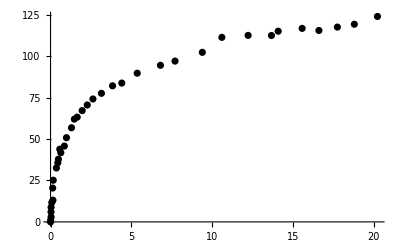

```mathematica
(*T=421-375*)
V02 = 0.80644;
bases2={91.209, 84.811, 80.123, 75.017, 70.384, 63.763, 61.902,55.44,48.188, 42.777, 35.23, 31.202, 24.775, 20.503, 17.955, 14.877, 12.53, 10.958, 9.554, 8.1781, 7.3875, 6.5969, 5.2109, 4.625, 3.6484, 3.3594, 2.9844, 2.8172, 2.4172, 1.5547, 1.3953, 1.47, 1.15, 0.95469, 0.94531, 0.96406, 0.83281, 0.80644};
amps2 = {123.91, 119.21, 117.5, 115.45, 116.72, 115.01, 112.43, 112.49, 111.31, 102.27, 96.986, 94.436, 89.673, 83.742, 82.081, 77.544, 74.137, 70.514, 67.129, 63.189, 61.991, 56.772, 50.766, 45.737, 41.728, 43.838, 37.803, 35.66, 32.523, 25.131, 20.402, 13.108, 11.699, 8.814, 5.9939, 2.9476, 0.97656, 0};
data2 = {(bases2-V02)/93 20.8, amps2}ᵀ;
ListPlot[data2, PlotStyle->Black]
```

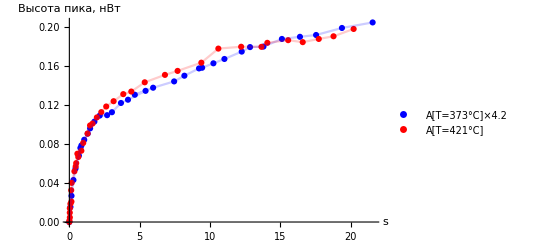

```mathematica
df1 = {(bases1-V01)/93 20.8, 4.2amps1 1.6/1000}ᵀ;
df2 = {(bases2-V02)/93 20.8, amps2 1.6/1000}ᵀ;
img  = Show[{
ListPlot[{df1,df2}, PlotStyle->{Blue, Red}, AxesLabel->{"s", "Высота пика, нВт"}, PlotLegends->{"A[T=373°C]×4.2", "A[T=421°C]"}],
ListLinePlot[{df1,df2}, PlotStyle->{{Opacity[0.2],Blue}, {Opacity[0.2], Red}}]
}]
(*Export[NotebookDirectory[]<>"figures/"<>"s_dep_1.pdf", img]*)
```

```mathematica
421-373
```

48

```mathematica
{Xexp, Yexp} =  {(bases2-V02)/93 20.8, amps2 1.6/1000};
```

## Подсчёт количества атомов

```mathematica
Ω = 2π 0.03;
ω = 2 π (3 10^8)/(670.9 10^-9);
(1 10^-9(*Вт*))/(ℏ ω)(4π)/Ω
```

2.25003×10^11